```mathematica
(* Guy F Mongelli                                ChE 400
Prof. Clark                                     10/18/2010   *)
```

This is a text cell..

```mathematica
(* Assignment #6   *)
```

```mathematica
(* Problem #1*)
```

```mathematica
a=1;
b=3;
```

```mathematica
f[x_]:=x^5;
g[x_]:=x^3;
p[x_]:=x^3;
```

```mathematica
(*Defining the functions that are prefactors to F[x] and F'[x], when the differential equation is of the form:
d/dx[f(x)*dF/dx]=-g(x)F
*)
```

```mathematica
Lambda[n_]:=4+(n*π)^2/(Log[3])^2
```

```mathematica
(* Defining the Full Eigenvalues for the system  *)
```

```mathematica
LambdaP[n_]:=(n π)^2/(Log[3])^2
```

```mathematica
(* Defining the coefficient of Ln[x] in the sine function *)
```

```mathematica
λ[n_]:=4+(n π^2)/(Log[3])^2
```

```mathematica
F[n_,x_]:=1/x^2 Sin[(n π Log[x])/Log[3]]
```

```mathematica
(* Defining F as the eigenfunctions of the differential equation*)
```

```mathematica
(* I plan to test the equality of the RSLS by substitutiing the eigenfunctions into the differential equation *)
```

```mathematica
G[n_,x_]=D[F[n,x],x]
```

(n π Cos[(n π Log[x])/Log[3]])/(x^3 Log[3])-(2 Sin[(n π Log[x])/Log[3]])/x^3

```mathematica
(* Part B *)
```

```mathematica
(*Defining the multiplicative factor of the trig function as Z[x]  *)
```

```mathematica
LambdaIntegral[n_]:=Simplify[(∫_a^b g[x](G[n,x])^2ⅆx)/(∫_a^b (F[n,x])^2g[x]ⅆx),Element[n,Integers]]
```

```mathematica
LambdaTable=Table[{N[LambdaIntegral[i],2]},{i,1,5}];
TableForm[LambdaTable]
```

3.7
14.
30.
53.
83.

```mathematica
(* As further proof that these integrals are positive  *)
```

```mathematica
(* What, if anything, is the lambda integral mean in the context of this problem ? Not sure it applies to anything...Consider it a vestigial code segment *)
```

```mathematica
Clear[n]
```

```mathematica
l[n_]=Simplify[(∫_1^3 x^3*(G[n,x])^2ⅆx)/(∫_1^3 x^2(F[n,x])^2ⅆx),Element[n,Integers]]
```

((4 n^2 π^2+Log[3]^2) (8 n^2 π^2+Log[3] Log[43046721]))/(48 Log[3]^2 (n^2 π^2+Log[3]^2))

```mathematica
N[l[4],2]
```

88.

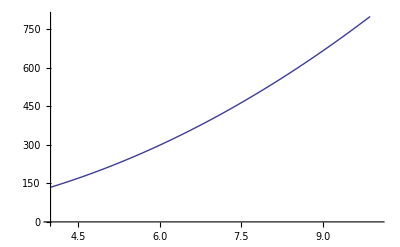

```mathematica
Plot[Lambda[n],{n,4,10},PlotRange->{0,800} ]
```

```mathematica
(* Part C  *)
```

```mathematica
∫_1^3 √(g[x]/f[x])ⅆx
```

Log[3]

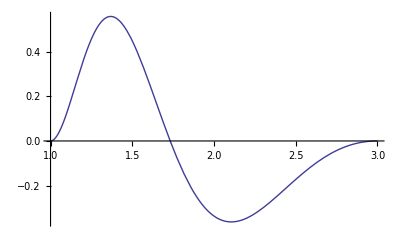

```mathematica
Plot[F[1,x]*g[x]*F[(1+1),x],{x,1,3}]
```

```mathematica
FullSimplify[∫_1^3 F[n,x]*g[x]*F[m,x]ⅆx,Element[{n,m},Integers]]
```

0

```mathematica
(*  This is zero, therefore the orthogonality of eigenfunctions is satisfied.  *)
```

```mathematica
(* Part D   *)
```

```mathematica
Element[n,Integers]
```

n∈Integers

```mathematica
G[n,1]
```

(n π)/Log[3]

```mathematica
G[n,3]
```

(n π Cos[n π])/(27 Log[3])-2/27 Sin[n π]

```mathematica
(* The following several lines of code are incomplete and not really relevant to the assignment *)
```

```mathematica
Simplify[D[x^5*G[n,x],x]]
```

-(x (n^2 π^2+4 Log[3]^2) Sin[(n π Log[x])/Log[3]])/Log[3]^2

```mathematica
Simplify[-λ[n]*x^3*F[n,x]]
```

x (-4-(n π^2)/Log[3]^2) Sin[(n π Log[x])/Log[3]]

```mathematica
LHS[x_]=Simplify[D[x^5*G[4,x],x]]
```

-(4 x (4 π^2+Log[3]^2) Sin[(4 π Log[x])/Log[3]])/Log[3]^2

```mathematica
RHS[x_]=Simplify[-λ[4]*x^3*F[4,x]]
```

x (-4-(4 π^2)/Log[3]^2) Sin[(4 π Log[x])/Log[3]]

```mathematica
FullSimplify[LHS[x]-RHS[x]]
```

-(12 π^2 x Sin[(4 π Log[x])/Log[3]])/Log[3]^2

```mathematica
(* Relevancy to assignment recommences *0
```

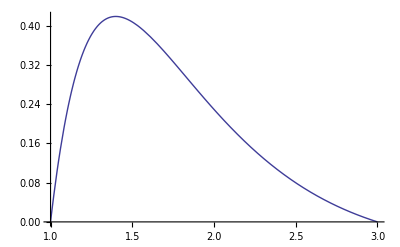

```mathematica
Plot[{F[1,x]},{x,1,3}]
```

```mathematica
(*  N is 1 above, and there are no interior nodes *)
```

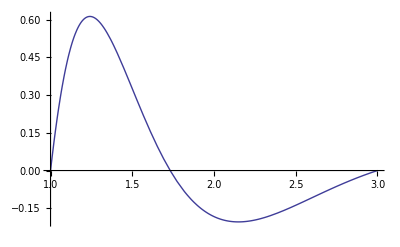

```mathematica
Plot[{F[2,x]},{x,1,3}]
```

```mathematica
(* N is 2 above and there is 1 interior node*)
```

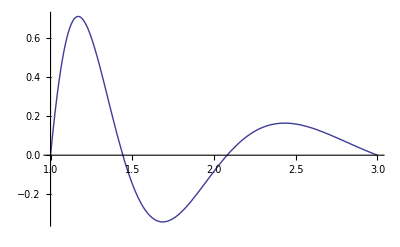

```mathematica
Plot[{F[3,x]},{x,1,3}]
```

```mathematica
(* N is 3 above, and there are two interior nodes *)
```

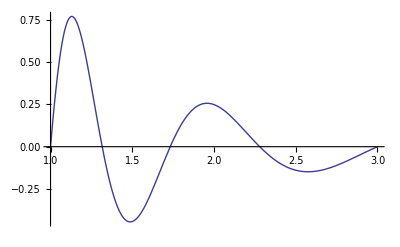

```mathematica
Plot[{F[4,x]},{x,1,3}]
```

```mathematica
(* N is 4 above and there are three interior nodes *)
```

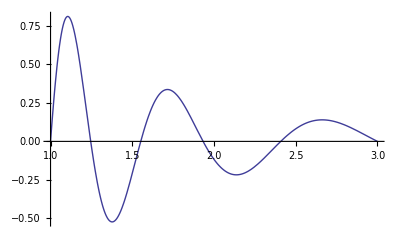

```mathematica
Plot[{F[5,x]},{x,1,3}]
```

```mathematica
(* N is 5 above and there are 4 interior nodes.*)
```

```mathematica
(*  The first five eigenfunction satisfy the (n-1) interior nodes rule artculated above *)
```

```mathematica
N[LambdaIntegral[1],10]
```

3.66860909

```mathematica
(* Part E*)
```

```mathematica
Z[x_]=Simplify[(g[x]/f[x])^(1/2),x>0]
```

1/x

```mathematica
(* Defining the fourier coefficients for the *)
```

```mathematica
cN[n_]=Simplify[(∫_1^3 Z[x]*(Sin[(n π Log[x])/Log[3]])ⅆx)/(∫_1^3 Z[x](Sin[(n π Log[x])/Log[3]])^2ⅆx),Element[n,Integers]]
```

-(2 (-1+(-1)^n))/(n π)

-(2 (-1+(-1)^n))/(n π)

-(2 (-1+(-1)^n))/(n π)

```mathematica
cN[1]
```

4/π

```mathematica
fapproxterm[x_,n_]:=cN[n]*1/x^2 Sin[(n π Log[x])/Log[3]]
```

```mathematica
fapprox[x_,k_]:=∑_(n=1)^k fapproxterm[x,n]
```

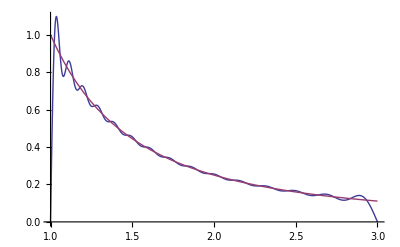

-Graphics-

```mathematica
Plot[{fapprox[x,30],1/x^2},{x,1,3}]
```

```mathematica
(*  The function is reasonable well defined bt this set of eigenfunctions on [1,3], with some misbehavior at the endpoints.  This misbehavior is mitigated by increasing the number of terms included in the approximation.  *)
```

```mathematica
(* Part F*)
```

```mathematica
Clear[a,b,m]
```

```mathematica
a=1;
b=4;
```

```mathematica
ym1[m_]=(-b+(b^2-4*a*m)^(.5))/(2a)
```

1/2 (-4+(16-4 m)^0.5)

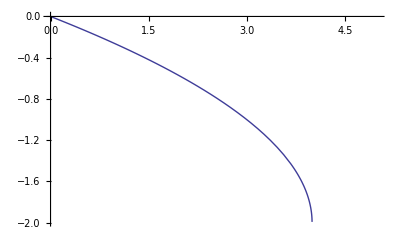

```mathematica
Plot[ym1[m],{m,0,5}]
```

```mathematica
m=0;
ymzero[m_]=(-b+(b^2-4*a*m)^(.5))/(2a)
```

0.

```mathematica
Clear[m]
```

```mathematica
ymzero[m_]=(-b+(b^2+4*a*m)^(.5))/(2a)
```

1/2 (-4+(16+4 m)^0.5)

```mathematica
y3[3]
```

y3[3]

```mathematica
Ff[x_]=Ax^y1[3]+Bx^y3[3]
```

Ax^y1[3]+Bx^y3[3]

```mathematica
FullSimplify[D[x^5*D[Ff[x],x],x]]
```

0

```mathematica
FullSimplify[-3*x^3*Ff[x]]
```

-3 (Ax^y1[3]+Bx^y3[3]) x^3

```mathematica
Solve[{Ff[1]==0,Ff[3]==0},{A,B}]
```

{{}}

```mathematica
(* This is the null set, indicating that A and B are zero  *)
```

```mathematica
(* Problem #2  *)
```

```mathematica
a=1;
b=3;
```

```mathematica
(* Problem #2 *)
```

```mathematica
G[t_,n_]:=Exp[-Lambda[n]*t]
```

```mathematica
G[0,5]
```

1

```mathematica
G[t,n]
```

ⅇ^(t (-4-(n^2 π^2)/Log[3]^2))

```mathematica
IotaTerm[x_,t_,n_]:=fapproxterm[x,n]*G[t,n]
```

```mathematica
IotaApprox[x_,t_,k_]:=∑_(n=1)^k IotaTerm[x,t,n]
```

```mathematica
fapprox[x,7]
```

(4 Sin[(π Log[x])/Log[3]])/(π x^2)+(4 Sin[(3 π Log[x])/Log[3]])/(3 π x^2)+(4 Sin[(5 π Log[x])/Log[3]])/(5 π x^2)+(4 Sin[(7 π Log[x])/Log[3]])/(7 π x^2)

```mathematica
IotaTerm[x,0,1]
```

(4 Sin[(π Log[x])/Log[3]])/(π x^2)

```mathematica
IotaApprox[x,0,5]
```

(4 Sin[(π Log[x])/Log[3]])/(π x^2)+(4 Sin[(3 π Log[x])/Log[3]])/(3 π x^2)+(4 Sin[(5 π Log[x])/Log[3]])/(5 π x^2)

```mathematica
N[fapprox[1.5,30],30]/IotaApprox[1.5,0,30]
```

1.

```mathematica
N[fapprox[2.5,30],30]/IotaApprox[2.5,0,30]
```

1.

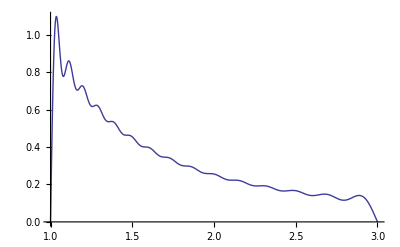

```mathematica
Plot[IotaApprox[x,0,30],{x,1,3}]
```

```mathematica
Manipulate[Plot[IotaApprox[x,t,30],{x,1,3}],{t,0,4}]
```

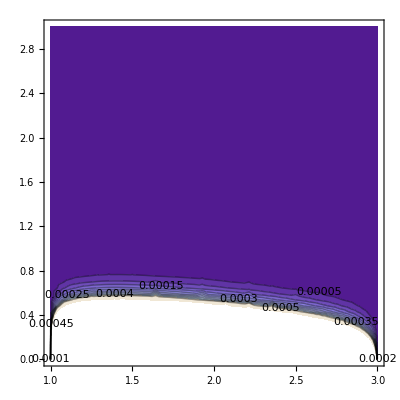

```mathematica
ContourPlot[IotaApprox[x,t,30],{x,1,3},{t,0,3},ContourLabels->True]
```

```mathematica
NSolve[IotaApprox[1.5,t,2]==10^-3,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.513356}}

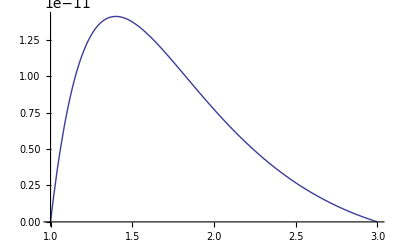

```mathematica
Plot[IotaApprox[x,2,30],{x,1,3},PlotRange->Automatic]
```

```mathematica
(* Part B *)
```

```mathematica
Tau[n_]=1/Lambda[n]
```

1/(4+(n^2 π^2)/Log[3]^2)

1/(4+(n^2 π^2)/Log[3]^2)

1/(4+(n^2 π^2)/Log[3]^2)

```mathematica
TauRatio[n_]:=(Lambda[1]/Lambda[n])
```

```mathematica
coeffs=Table[{N[Tau[i],3],N[TauRatio[i],3]},{i,1,20}];
TableForm[coeffs]
```

0.0821 | 1.
0.0272 | 0.332
0.0129 | 0.157
0.00742 | 0.0903
0.0048 | 0.0584
0.00335 | 0.0408
0.00247 | 0.0301
0.0019 | 0.0231
0.0015 | 0.0183
0.00122 | 0.0148
0.00101 | 0.0123
0.000846 | 0.0103
0.000722 | 0.00879
0.000622 | 0.00758
0.000542 | 0.0066
0.000477 | 0.00581
0.000422 | 0.00514
0.000377 | 0.00459
0.000338 | 0.00412
0.000305 | 0.00372

```mathematica
(* In this case, it is required to include the fist ten terms to reduce the error of dropping a term to less than 1 %.  However, for times greater than .0821 seconds, the first term is a satisfactory approximation. From a mathematical approach this makes sense, however, form observation of the values of Iota in the above contour plot, Iota goes to zero for times greater than 2 seconds.  *)
```

```mathematica
(* Challenge Problem *)
```

```mathematica
(* Part C *)
```

```mathematica
L=1
```

1

```mathematica
y[x_]:=Sin[n π x/L]
```

```mathematica
y'[x]
```

n π Cos[n π x]

```mathematica
z[x_]=x(1-x)
```

(1-x) x

```mathematica
clear[n,Lambda1]
```

clear[n,Lambda1]

```mathematica
Normalize[n_]=Simplify[∫_0^1 (Sin[n π x])^2ⅆx,Element[n,Integers]]
```

1/2

```mathematica
Lambda2[n_]:=Simplify[(∫_0^1 (x(1-x))Sin[n π x]ⅆx)/(∫_0^1 x(1-x)(Sin[n π x])^2ⅆx),Element[n,Integers]]
```

```mathematica
JTable=Table[{Normalize[i],Lambda2[i]},{i,1,5}];
TableForm[JTable]
```

1 | 48/(3 π+π^3)
1 | 0
1 | 16/(3 π+9 π^3)
1 | 0
1 | 48/(15 π+125 π^3)

```mathematica
Normalize[n_]=Simplify[∫_0^1 (Sin[n π x])^2ⅆx,Element[n,Integers]]
```

1/2

```mathematica
LambdaUpper=N[(∑_(n=1)^∞ (n π)^2(Lambda2[n])^2*Normalize[n])/(∑_(n=1)^∞ (Lambda2[n])^2*Normalize[n]),5]
```

10.079

```mathematica
(* This is the upper bound on lambda one as given by the eigenfunctions of the solved equation *)
```

```mathematica
Trial[a_,x_]=Expand[x(1-x)+a*x^2(1-x)^2]
```

x-2 x^3+x^4

```mathematica
Nn[n_]=∫_0^1 (Sin[(n π x)/1])^2ⅆx
```

1/2

```mathematica
Lambda3[n_,a_]:=FullSimplify[ ∫_0^1 (x(1-x)+a*x^2(1-x)^2)Sin[n π x]ⅆx  ,Element[n,Integers]]
```

```mathematica
JTable=Table[{Normalize[i],N[Lambda3[i,a],2],N[Lambda3[i,a]/Lambda3[1,a],2]},{i,1,5}];
TableForm[JTable]
```

1 | 0.0033 (-39. (-1.+a)+48. a) | 1.
1 | 0 | 0
1 | 0.00016 (-30. (-1.+a)+4. a) | (0.049 (-30. (-1.+a)+4. a))/(-39. (-1.+a)+48. a)
1 | 0 | 0
1 | 1.×10^-6 (-990. (-1.+a)+48. a) | (0.00032 (-990. (-1.+a)+48. a))/(-39. (-1.+a)+48. a)

```mathematica
Clear[a]
```

```mathematica
Simplify[D[(560 (-1+(-1)^n) n π (-12 a+(-1+a) n^2 π^2))/(a (1575-105 n^2 π^2+n^6 π^6)),a]]
```

(560 (-1+(-1)^n) n^3 π^3)/(a^2 (1575-105 n^2 π^2+n^6 π^6))

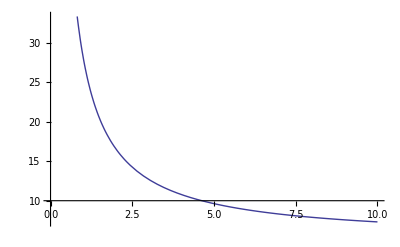

```mathematica
n=1;
Plot[{((560 (-1+(-1)^n) n π (-12 a+(-1+a) n^2 π^2))/(a (1575-105 n^2 π^2+n^6 π^6)))},{a,0,10}]
```

```mathematica
(* Coefficients drop off as a-squared.  Therefore, include only the first five terms *)
```

```mathematica
Normalize[n]∫_0^1 (x(1-x)a*x^2(1-x)^2)(Sin[n π x])^2ⅆx
```

```mathematica
LambdaUpper1[a_]:=N[(∑_(n=1)^5 (n π)^2(Lambda3[n,a])^2*Normalize[n])/(∑_(n=1)^5 (Lambda3[n,a])^2*Normalize[n]),1]
```

```mathematica
LambdaUpper1[.01]
```

9.99023

```mathematica
(*This upper limit on the first eigenvalue is closer in numberical value to the actual eigenvalue, therefore (in general), increasing the complixity of the trial function will produce bettetr approximations of the system  *)
```

```mathematica
FindRoot[D[LambdaUpper1[a],a],{a,1}]
```

{a→1.14005}

```mathematica
a=1.1400480466222032
```

1.14005